Evaluate the evaluation cells of the other important notebooks

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"directMat-2.nb",EvaluationElements->Automatic];
NotebookEvaluate[NotebookDirectory[]<>"periods.nb",EvaluationElements->Automatic];
NotebookEvaluate[NotebookDirectory[]<>"WeylTest.nb",EvaluationElements->Automatic];
```

Given some function f_L[k,l] generate the corresponding matrix

```mathematica
DirectFMat[L_,f_]:=Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[k,l]]=f[L,k,l];
,{k,1,L},{l,1,L}];
Return[tempMat,Module];
]
```

```mathematica
DirectFMatN[L_,f_,NPrec_]:=
Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[k,l]]=N[f[L,k,l],NPrec];
,{k,1,L},{l,1,L}];
Return[tempMat,Module];
]
```

C matrix  for X_m X_n , which computes ∂^m X ∂^n X one point function on the disk when m,n are positive integer.

```mathematica
DirectCMat[L_,m_,n_]:=DirectFMat[L,(((Abs[m]!)(Abs[n]!))/#1^2 Exp[-I*2*Pi*(m*#2+n*#3)/#1])&]
DirectCMatN[L_,m_,n_,NPrec_]:=DirectFMatN[L,(((Abs[m]!)(Abs[n]!))/#1^2 Exp[-I*2*Pi*(m*#2+n*#3)/#1])&,NPrec]
```

```mathematica
DirectTracedCMat[L_,m_,n_,l1_,l2_]:=
DirectTracedMat[L,l1,l2,DirectCMat[L,m,n]]
```

```mathematica
DirectTracedCMatN[L_,m_,n_,l1_,l2_,NPrec_]:=
DirectTracedMat[L,l1,l2,DirectCMatN[L,m,n,NPrec]]
```

### Generate Analytic Formula For ∂^n X ∂X

Compute the disk one point function by the conformal transformation of one point function on the torus

```mathematica
Ord=4;
u[z_]:=Integrate[fHatS[a],{a,0,z}]
uTrun[z_]:=Series[u[z],{z,0,Ord+3}]
T2=Simplify[Series[fHatS[z]Conjugate[fHatS[0]] (-1/(2Im[τ]))+1/(2Pi),{z,0,Ord}],Assumptions->Table[Derivative[2k-1][fHatS][0]==0,{k,1,Ord+3}]];
D2=Sum[1/(n!)z^n CorrelatorD2[n],{n,0,Ord}];
T2List=CoefficientList[T2,z];
MatchingList=Simplify[MapIndexed[#1*Factorial[First[#2]-1]&,T2List]]
```

{1/2 (1/π-(Conjugate[fHatS[0]] fHatS[0])/Im[τ]),0,-(Conjugate[fHatS[0]] fHatS''[0])/(2 Im[τ]),0,-(Conjugate[fHatS[0]] fHatS^(4)[0])/(2 Im[τ])}

### Calculating tr(CA^-1):

```mathematica
setL=310;
prec=15;
AMat=DirectMatN[setL,prec];
```

FindTrCA has the input (L,l1,l2) as usual.  s is an integer indicating that it is computing :∂^s X OverBar[∂]X:  on the disk.  
One has to input the correct CMat for :∂^s X OverBar[∂]X:  to get the correct matching.
The output is {τ, Analytic result for one point function, numerical result for one-point function}

```mathematica
findTrCA[L_,l1_,l2_,s_,AMat_,CMat_]:=Module[{l3,redA,invA,redC,tr,f,DerList,fHat,f0,df,ddf,per,perRed,AnalyticTest,NumericalTest,Formula,ReplaceTable},
l3=L/2-l1-l2;
(*Print[1];*)
redA=DirectRedTracedMat[L,l1,l2,AMat];
(*Print[1];*)
redC=DirectRedTracedMat[L,l1,l2,CMat];
(*Print[2];*)
invA=Inverse[redA];
(*Print[3]*)
f=CylEqnFastOptimized[l1,l2,l3,z];
(*Print[4];*)
NumericalTest=Tr[redC . invA];
per=PeriodsFastGivenF[l1,l2,l3,l1/2,l2/2,l3/2,f,z]//N;
perRed=per/per[[1]];
fHat=f/per[[1]];
(*Print[1/(1-perRed[[2]])];*)
DerList=Table[D[fHat,{z,n}]/.{z->0},{n,0,s+1}];
ReplaceTable=Join[{fHatS[0]->DerList[[1]]},Table[{Derivative[n][fHatS][0]->DerList[[n+1]]},{n,1,s+1}]]//Flatten;
AnalyticTest=MatchingList[[s]]/.ReplaceTable/.{τ->perRed[[2]],z->0}//N;
(*Note that 1/per[[1]] is \hat{f}(0)*)
Return[{perRed[[2]],AnalyticTest,NumericalTest},Module]
]
```

Test Timing

```mathematica
findTrCA[setL,3,3,1,AMat,CMat11]//Timing
```

{1.66645,{0.934524+0.355899 ⅈ,0.0740177+0. ⅈ,0.08557485569812+0. ⅈ}}

Compute  :∂X∂X: one point function

```mathematica
CMat11=DirectCMatN[setL,1,-1,prec];
```

```mathematica
(*Since we want to test different τ at the same L, useful to store the precursor matrices*)

L1=Table[
Print[k];
findTrCA[setL,k,k,1,AMat,CMat11]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,-0.0631518+0. ⅈ,0.1018635688656+0. ⅈ},{0.934524+0.355899 ⅈ,-0.0740177+0. ⅈ,0.08557485569812+0. ⅈ},{0.916834+0.399269 ⅈ,-0.0842269+0. ⅈ,0.07545780579988+0. ⅈ},{0.900453+0.434952 ⅈ,-0.0920559+0. ⅈ,0.06741244951662+0. ⅈ},{0.885045+0.465505 ⅈ,-0.0989291+0. ⅈ,0.06051690181521+0. ⅈ},{0.869982+0.493084 ⅈ,-0.104983+0. ⅈ,0.05439788645377+0. ⅈ},{0.855128+0.518417 ⅈ,-0.110497+0. ⅈ,0.04886568687005+0. ⅈ},{0.840281+0.542151 ⅈ,-0.11552+0. ⅈ,0.04381100575745+0. ⅈ},{0.825372+0.56459 ⅈ,-0.120153+0. ⅈ,0.03916566152921+0. ⅈ},{0.810299+0.586017 ⅈ,-0.124414+0. ⅈ,0.03488471175527+0. ⅈ},{0.795015+0.60659 ⅈ,-0.128352+0. ⅈ,0.03093728946557+0. ⅈ},{0.779455+0.626458 ⅈ,-0.131975+0. ⅈ,0.0273014776544+0. ⅈ},{0.76358+0.645713 ⅈ,-0.135308+0. ⅈ,0.02396124390897+0. ⅈ},{0.747341+0.664441 ⅈ,-0.138355+0. ⅈ,0.02090450652791+0. ⅈ},{0.730699+0.6827 ⅈ,-0.141132+0. ⅈ,0.01812185964157+0. ⅈ},{0.713611+0.700542 ⅈ,-0.143641+0. ⅈ,0.0156057009055+0. ⅈ},{0.696039+0.718004 ⅈ,-0.145893+0. ⅈ,0.01334961497881+0. ⅈ},{0.677937+0.73512 ⅈ,-0.14789+0. ⅈ,0.01134792486426+0. ⅈ},{0.659265+0.75191 ⅈ,-0.149639+0. ⅈ,0.009595356298635+0. ⅈ},{0.639976+0.768395 ⅈ,-0.151144+0. ⅈ,0.008086779730948+0. ⅈ},{0.620023+0.784584 ⅈ,-0.152412+0. ⅈ,0.006817006072345+0. ⅈ},{0.599352+0.800486 ⅈ,-0.153446+0. ⅈ,0.00578061954352+0. ⅈ},{0.577907+0.816102 ⅈ,-0.154254+0. ⅈ,0.00497183532719+0. ⅈ},{0.555628+0.831431 ⅈ,-0.15484+0. ⅈ,0.00438437231946+0. ⅈ},{0.532446+0.846464 ⅈ,-0.155212+0. ⅈ,0.00401133258433+0. ⅈ},{0.508285+0.861189 ⅈ,-0.155378+0. ⅈ,0.00384507938622+0. ⅈ},{0.483062+0.875586 ⅈ,-0.155346+0. ⅈ,0.00387710492509+0. ⅈ},{0.456679+0.889632 ⅈ,-0.155126+0. ⅈ,0.00409787692275+0. ⅈ},{0.429026+0.903292 ⅈ,-0.154728+0. ⅈ,0.00449664949881+0. ⅈ},{0.399976+0.916526 ⅈ,-0.154164+0. ⅈ,0.00506121730757+0. ⅈ},{0.369374+0.929281 ⅈ,-0.153449+0. ⅈ,0.005777580689888+0. ⅈ},{0.337039+0.941491 ⅈ,-0.152599+0. ⅈ,0.006629469628292+0. ⅈ},{0.302741+0.953073 ⅈ,-0.151634+0. ⅈ,0.007597637139246+0. ⅈ},{0.266188+0.963921 ⅈ,-0.150575+0. ⅈ,0.008658759256466+0. ⅈ},{0.226986+0.973898 ⅈ,-0.149454+0. ⅈ,0.009783621494596+0. ⅈ},{0.184568+0.98282 ⅈ,-0.14831+0. ⅈ,0.01093389870569+0. ⅈ},{0.138028+0.990428 ⅈ,-0.147197+0. ⅈ,0.01205582323729+0. ⅈ},{0.0856363+0.996326 ⅈ,-0.146204+0. ⅈ,0.0130658137977+0. ⅈ},{0.0222687+0.999752 ⅈ,-0.145519+0. ⅈ,0.01382147930283+0. ⅈ}}

x axis is Reτ, y axis is the real part of the 1 point function

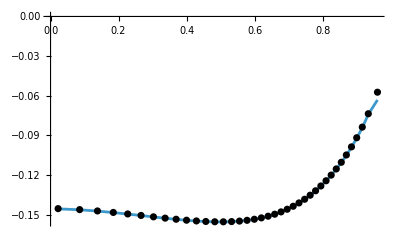

```mathematica
Show[ListLinePlot[Re[L1[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L1],PlotStyle->{Black}]]
```

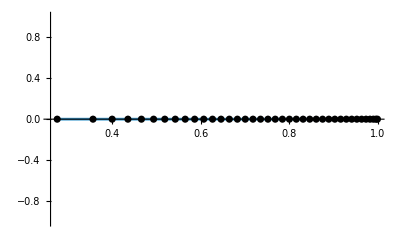

```mathematica
Show[ListLinePlot[Im[L1[[All,{1,2}]]]],ListPlot[Im[L1[[All,{1,3}]]],PlotStyle->{Black}]]
```

```mathematica
CMat21=DirectCMatN[setL,2,-1,prec];
```

```mathematica
L12=Table[
Print[k];
findTrCA[setL,k,k,2,AMat,CMat21]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,0.,0.+0. ⅈ},{0.934524+0.355899 ⅈ,0.,0.+0. ⅈ},{0.916834+0.399269 ⅈ,0.,0.+0. ⅈ},{0.900453+0.434952 ⅈ,0.,0.+0. ⅈ},{0.885045+0.465505 ⅈ,0.,0.+0. ⅈ},{0.869982+0.493084 ⅈ,0.,0.+0. ⅈ},{0.855128+0.518417 ⅈ,0.,0.+0. ⅈ},{0.840281+0.542151 ⅈ,0.,0.+0. ⅈ},{0.825372+0.56459 ⅈ,0.,0.+0. ⅈ},{0.810299+0.586017 ⅈ,0.,0.+0. ⅈ},{0.795015+0.60659 ⅈ,0.,0.+0. ⅈ},{0.779455+0.626458 ⅈ,0.,0.+0. ⅈ},{0.76358+0.645713 ⅈ,0.,0.+0. ⅈ},{0.747341+0.664441 ⅈ,0.,0.+0. ⅈ},{0.730699+0.6827 ⅈ,0.,0.+0. ⅈ},{0.713611+0.700542 ⅈ,0.,0.+0. ⅈ},{0.696039+0.718004 ⅈ,0.,0.+0. ⅈ},{0.677937+0.73512 ⅈ,0.,0.+0. ⅈ},{0.659265+0.75191 ⅈ,0.,0.+0. ⅈ},{0.639976+0.768395 ⅈ,0.,0.+0. ⅈ},{0.620023+0.784584 ⅈ,0.,0.+0. ⅈ},{0.599352+0.800486 ⅈ,0.,0.+0. ⅈ},{0.577907+0.816102 ⅈ,0.,0.+0. ⅈ},{0.555628+0.831431 ⅈ,0.,0.+0. ⅈ},{0.532446+0.846464 ⅈ,0.,0.+0. ⅈ},{0.508285+0.861189 ⅈ,0.,0.+0. ⅈ},{0.483062+0.875586 ⅈ,0.,0.+0. ⅈ},{0.456679+0.889632 ⅈ,0.,0.+0. ⅈ},{0.429026+0.903292 ⅈ,0.,0.+0. ⅈ},{0.399976+0.916526 ⅈ,0.,0.+0. ⅈ},{0.369374+0.929281 ⅈ,0.,0.+0. ⅈ},{0.337039+0.941491 ⅈ,0.,0.+0. ⅈ},{0.302741+0.953073 ⅈ,0.,0.+0. ⅈ},{0.266188+0.963921 ⅈ,0.,0.+0. ⅈ},{0.226986+0.973898 ⅈ,0.,0.+0. ⅈ},{0.184568+0.98282 ⅈ,0.,0.+0. ⅈ},{0.138028+0.990428 ⅈ,0.,0.+0. ⅈ},{0.0856363+0.996326 ⅈ,0.,0.+0. ⅈ},{0.0222687+0.999752 ⅈ,0.,0.+0. ⅈ}}

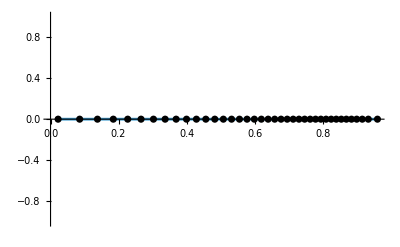

```mathematica
Show[ListLinePlot[Re[L12[[All,{1,2}]]]],ListPlot[Re[L12[[All,{1,3}]]],PlotStyle->{Black}]]
```

```mathematica
Show[ListLinePlot[Im[L12[[All,{1,2}]]]],ListPlot[Im[L12[[All,{1,3}]]],PlotStyle->{Black}]]
```

-Graphics-

```mathematica
CMat31=DirectCMatN[setL,3,-1,prec];
```

```mathematica
L13=Table[
Print[k];
findTrCA[setL,k,k,3,AMat,CMat31]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,-0.126018+0.00767201 ⅈ,-0.1143451040926+0.00696133762325 ⅈ},{0.934524+0.355899 ⅈ,-0.145806+0.0208267 ⅈ,-0.1449956542448+0.020710901593 ⅈ},{0.916834+0.399269 ⅈ,-0.161924+0.0367115 ⅈ,-0.160986134082+0.0364989079828 ⅈ},{0.900453+0.434952 ⅈ,-0.170706+0.0535593 ⅈ,-0.1702310337939+0.05341033141828 ⅈ},{0.885045+0.465505 ⅈ,-0.174823+0.0708622 ⅈ,-0.1744357605322+0.07070520674191 ⅈ},{0.869982+0.493084 ⅈ,-0.174568+0.0878357 ⅈ,-0.1743347521101+0.08771814297166 ⅈ},{0.855128+0.518417 ⅈ,-0.170582+0.103939 ⅈ,-0.1704119053596+0.1038355921891 ⅈ},{0.840281+0.542151 ⅈ,-0.163193+0.118567 ⅈ,-0.1630981890349+0.1184977705745 ⅈ},{0.825372+0.56459 ⅈ,-0.152897+0.131258 ⅈ,-0.1528398600684+0.1312087161036 ⅈ},{0.810299+0.586017 ⅈ,-0.140141+0.141568 ⅈ,-0.1401212983301+0.141548555616 ⅈ},{0.795015+0.60659 ⅈ,-0.125469+0.149187 ⅈ,-0.1254678248295+0.1491852544943 ⅈ},{0.779455+0.626458 ⅈ,-0.109425+0.153866 ⅈ,-0.1094381634393+0.1538843398497 ⅈ},{0.76358+0.645713 ⅈ,-0.0925932+0.155486 ⅈ,-0.0926110353578+0.1555156721579 ⅈ},{0.747341+0.664441 ⅈ,-0.0755488+0.154017 ⅈ,-0.07556841668305+0.154056695136 ⅈ},{0.730699+0.6827 ⅈ,-0.0588604+0.149549 ⅈ,-0.05887716007421+0.149591857255 ⅈ},{0.713611+0.700542 ⅈ,-0.0430572+0.142265 ⅈ,-0.04307028520459+0.1423081206909 ⅈ},{0.696039+0.718004 ⅈ,-0.0286207+0.132448 ⅈ,-0.0286290171928+0.1324866721251 ⅈ},{0.677937+0.73512 ⅈ,-0.0159622+0.120459 ⅈ,-0.0159664897188+0.1204911287561 ⅈ},{0.659265+0.75191 ⅈ,-0.00541267+0.106729 ⅈ,-0.00541388374307+0.1067526908354 ⅈ},{0.639976+0.768395 ⅈ,0.00278991+0.0917374 ⅈ,0.002790375933+0.09175282549789 ⅈ},{0.620023+0.784584 ⅈ,0.00850713+0.0759972 ⅈ,0.00850790246432+0.07600417167506 ⅈ},{0.599352+0.800486 ⅈ,0.0117038+0.0600302 ⅈ,0.0117038118786+0.06003042894384 ⅈ},{0.577907+0.816102 ⅈ,0.0124475+0.0443505 ⅈ,0.0124462514979+0.04434603169144 ⅈ},{0.555628+0.831431 ⅈ,0.0109044+0.0294428 ⅈ,0.0109020500968+0.0294364126063 ⅈ},{0.532446+0.846464 ⅈ,0.00733129+0.0157451 ⅈ,0.00732872262979+0.0157396262132 ⅈ},{0.508285+0.861189 ⅈ,0.00206425+0.00363183 ⅈ,0.0020632284822+0.00363003524584 ⅈ},{0.483062+0.875586 ⅈ,-0.00449491-0.00659966 ⅈ,-0.00449196423187-0.00659533745692 ⅈ},{0.456679+0.889632 ⅈ,-0.0118947-0.0147395 ⅈ,-0.0118848165364-0.0147273178765 ⅈ},{0.429026+0.903292 ⅈ,-0.0196509-0.0206727 ⅈ,-0.0196308394362-0.020651631358 ⅈ},{0.399976+0.916526 ⅈ,-0.0272639-0.0243822 ⅈ,-0.0272304528927-0.0243523527675 ⅈ},{0.369374+0.929281 ⅈ,-0.0342352-0.0259495 ⅈ,-0.03418548892093-0.0259118142725 ⅈ},{0.337039+0.941491 ⅈ,-0.0400817-0.0255507 ⅈ,-0.04001351430704-0.0255072584169 ⅈ},{0.302741+0.953073 ⅈ,-0.0443461-0.0234513 ⅈ,-0.04425820151033-0.0234048062049 ⅈ},{0.266188+0.963921 ⅈ,-0.0466003-0.0199978 ⅈ,-0.04649297359964-0.0199517063012 ⅈ},{0.226986+0.973898 ⅈ,-0.0464375-0.0156105 ⅈ,-0.04631263964936-0.0155685106438 ⅈ},{0.184568+0.98282 ⅈ,-0.0434392-0.0107787 ⅈ,-0.0433006230439-0.0107442840881 ⅈ},{0.138028+0.990428 ⅈ,-0.0370821-0.00606599 ⅈ,-0.03693515862859-0.00604195861468 ⅈ},{0.0856363+0.996326 ⅈ,-0.0264376-0.00214809 ⅈ,-0.0262851927505-0.0021357101771 ⅈ},{0.0222687+0.999752 ⅈ,-0.00855393+0. ⅈ,-0.00824362965989+0. ⅈ}}

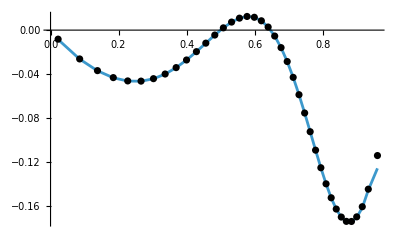

```mathematica
Show[ListLinePlot[Re[L13[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L13],PlotStyle->{Black}]]
```

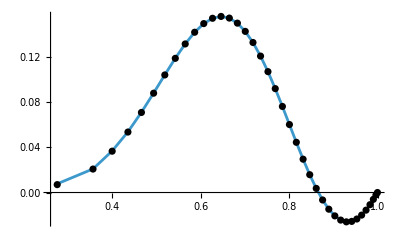

```mathematica
Show[ListLinePlot[Im[L13[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L13],PlotStyle->{Black}]]
```

```mathematica
CMat41=DirectCMatN[setL,4,-1,prec];
L4=Table[
Print[k];
findTrCA[setL,k,k,4,AMat,CMat41]
,{k,1,41,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

{{0.96148+0.274875 ⅈ,0.,0.+0. ⅈ},{0.934524+0.355899 ⅈ,0.,0.+0. ⅈ},{0.916834+0.399269 ⅈ,0.,0.+0. ⅈ},{0.900453+0.434952 ⅈ,0.,0.+0. ⅈ},{0.885045+0.465505 ⅈ,0.,0.+0. ⅈ},{0.869982+0.493084 ⅈ,0.,0.+0. ⅈ},{0.855128+0.518417 ⅈ,0.,0.+0. ⅈ},{0.840281+0.542151 ⅈ,0.,0.+0. ⅈ},{0.825372+0.56459 ⅈ,0.,0.+0. ⅈ},{0.810299+0.586017 ⅈ,0.,0.+0. ⅈ},{0.795015+0.60659 ⅈ,0.,0.+0. ⅈ},{0.779455+0.626458 ⅈ,0.,0.+0. ⅈ},{0.76358+0.645713 ⅈ,0.,0.+0. ⅈ},{0.747341+0.664441 ⅈ,0.,0.+0. ⅈ},{0.730699+0.6827 ⅈ,0.,0.+0. ⅈ},{0.713611+0.700542 ⅈ,0.,0.+0. ⅈ},{0.696039+0.718004 ⅈ,0.,0.+0. ⅈ},{0.677937+0.73512 ⅈ,0.,0.+0. ⅈ},{0.659265+0.75191 ⅈ,0.,0.+0. ⅈ},{0.639976+0.768395 ⅈ,0.,0.+0. ⅈ},{0.620023+0.784584 ⅈ,0.,0.+0. ⅈ}}

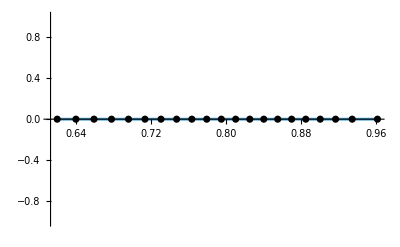

```mathematica
Show[ListLinePlot[Re[L4[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L4],PlotStyle->{Black}]]
```

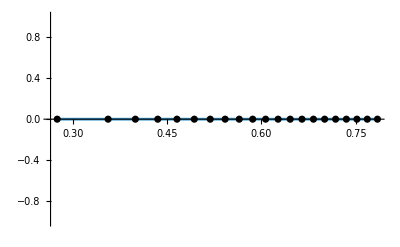

```mathematica
Show[ListLinePlot[Im[L4[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L4],PlotStyle->{Black}]]
```

```mathematica
CMat51=DirectCMatN[setL,5,-1,prec];
```

```mathematica
L5=Table[
Print[k];
findTrCA[setL,k,k,5,AMat,CMat51]
,{k,1,41,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

{{0.96148+0.274875 ⅈ,-1.5026+0.183637 ⅈ,-1.36378136114+0.166671951894 ⅈ},{0.934524+0.355899 ⅈ,-1.67957+0.489808 ⅈ,-1.671297913409+0.487394152718 ⅈ},{0.916834+0.399269 ⅈ,-1.74588+0.834553 ⅈ,-1.737402780059+0.830500414219 ⅈ},{0.900453+0.434952 ⅈ,-1.66239+1.15706 ⅈ,-1.65975933501+1.155226591725 ⅈ},{0.885045+0.465505 ⅈ,-1.47295+1.42884 ⅈ,-1.471786031136+1.42770670798 ⅈ},{0.869982+0.493084 ⅈ,-1.20311+1.62113 ⅈ,-1.203450197848+1.621591188411 ⅈ},{0.855128+0.518417 ⅈ,-0.886566+1.7184 ⅈ,-0.8872698947558+1.719766573009 ⅈ},{0.840281+0.542151 ⅈ,-0.556699+1.71334 ⅈ,-0.557453469061+1.715665364469 ⅈ},{0.825372+0.56459 ⅈ,-0.246777+1.61088 ⅈ,-0.247194871613+1.613602897387 ⅈ},{0.810299+0.586017 ⅈ,0.0144424+1.42507 ⅈ,0.01447168973+1.42796050587 ⅈ},{0.795015+0.60659 ⅈ,0.205084+1.17861 ⅈ,0.205545577176+1.181256758924 ⅈ},{0.779455+0.626458 ⅈ,0.312422+0.899109 ⅈ,0.313188833908+0.9013160540987 ⅈ},{0.76358+0.645713 ⅈ,0.333938+0.616277 ⅈ,0.334800061048+0.617868782849 ⅈ},{0.747341+0.664441 ⅈ,0.277136+0.35803 ⅈ,0.277881945211+0.358993877321 ⅈ},{0.730699+0.6827 ⅈ,0.15828+0.147432 ⅈ,0.15871435125+0.147836552855 ⅈ},{0.713611+0.700542 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.696039+0.718004 ⅈ,-0.171743-0.0778595 ⅈ,-0.172219362233-0.0780754070487 ⅈ},{0.677937+0.73512 ⅈ,-0.331078-0.0893117 ⅈ,-0.331986981627-0.0895569107153 ⅈ},{0.659265+0.75191 ⅈ,-0.455543-0.0463242 ⅈ,-0.456765013854-0.046448462032 ⅈ},{0.639976+0.768395 ⅈ,-0.528887+0.0321987 ⅈ,-0.530262317483+0.032282405532 ⅈ},{0.620023+0.784584 ⅈ,-0.543056+0.123122 ⅈ,-0.544407387467+0.123428488134 ⅈ}}

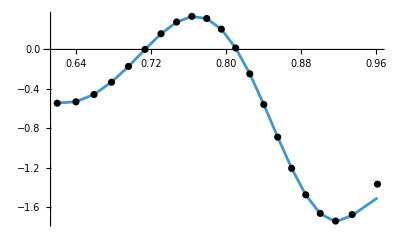

```mathematica
Show[ListLinePlot[Re[L5[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L5],PlotStyle->{Black}]]
```

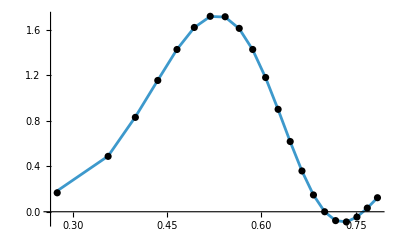

```mathematica
Show[ListLinePlot[Im[L5[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L5],PlotStyle->{Black}]]
```

```mathematica
(*SAME exact {l1,l2,l3} as above but in a different order, so τ will be different (related by modular transformation). 
Note that tr(CA^{-1}) is still the same but tr(CA^{-1})/|\hat{f}(0)|^2 is not*)
L2=Table[
Print[k];
findTrCA[setL,setL/2-2k,k,AMat,CMat]
,{k,1,77,2}]
```

1

0.10184264651987+0.00206446406121 ⅈ

{1.+0. ⅈ,0.474144+3.38345 ⅈ,-0.474144+3.38345 ⅈ}

3

0.08513571053264+0.008657455580628 ⅈ

{1.+0. ⅈ,0.501515+2.72603 ⅈ,-0.501515+2.72603 ⅈ}

5

0.07420525664148+0.01368832147399 ⅈ

{1.+0. ⅈ,0.499669+2.39884 ⅈ,-0.499669+2.39884 ⅈ}

7

0.0650838154281+0.01755703015441 ⅈ

{1.+0. ⅈ,0.500116+2.18517 ⅈ,-0.500116+2.18517 ⅈ}

9

0.05695474068454+0.02043979193584 ⅈ

{1.+0. ⅈ,0.499948+2.02452 ⅈ,-0.499948+2.02452 ⅈ}

11

0.04953348875168+0.02245593786133 ⅈ

{1.+2.77556×10^-17 ⅈ,0.500027+1.89631 ⅈ,-0.500027+1.89631 ⅈ}

13

0.04270577552107+0.02370363913933 ⅈ

{1.-2.77556×10^-17 ⅈ,0.499984+1.78917 ⅈ,-0.499984+1.78917 ⅈ}

15

0.03642567566391+0.02427217063605 ⅈ

{1.+0. ⅈ,0.50001+1.69724 ⅈ,-0.50001+1.69724 ⅈ}

17

0.03067688236962+0.02424677854662 ⅈ

{1.+0. ⅈ,0.499994+1.61653 ⅈ,-0.499994+1.61653 ⅈ}

19

0.02545517064104+0.02371055074899 ⅈ

{1.-5.55112×10^-17 ⅈ,0.500005+1.54459 ⅈ,-0.500005+1.54459 ⅈ}

21

0.02075954320862+0.02274488541728 ⅈ

{1.+0. ⅈ,0.499997+1.47958 ⅈ,-0.499997+1.47958 ⅈ}

23

0.0165874749779+0.02142925101792 ⅈ

{1.+0. ⅈ,0.500002+1.42026 ⅈ,-0.500002+1.42026 ⅈ}

25

0.01293232077974+0.01984058166076 ⅈ

{1.+0. ⅈ,0.499998+1.3656 ⅈ,-0.499998+1.3656 ⅈ}

27

0.00978197548696+0.01805249756845 ⅈ

{1.+0. ⅈ,0.500001+1.3149 ⅈ,-0.500001+1.3149 ⅈ}

29

0.007118317126345+0.01613446471562 ⅈ

{1.+5.55112×10^-17 ⅈ,0.499999+1.26754 ⅈ,-0.499999+1.26754 ⅈ}

31

0.00491717062411+0.01415096690692 ⅈ

{1.-5.55112×10^-17 ⅈ,0.500001+1.22306 ⅈ,-0.500001+1.22306 ⅈ}

33

0.00314863363078+0.01216073959511 ⅈ

{1.-5.55112×10^-17 ⅈ,0.499999+1.18108 ⅈ,-0.499999+1.18108 ⅈ}

35

0.0017776609837+0.01021609942145 ⅈ

{1.+5.55112×10^-17 ⅈ,0.500001+1.14127 ⅈ,-0.500001+1.14127 ⅈ}

37

0.000764835205049+0.008362392872289 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+1.10337 ⅈ,-0.5+1.10337 ⅈ}

39

0.000067268662097+0.0066375796156 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+1.06715 ⅈ,-0.5+1.06715 ⅈ}

41

-0.00036040549528+0.005071959987812 ⅈ

{1.+0. ⅈ,0.5+1.03241 ⅈ,-0.5+1.03241 ⅈ}

43

-0.000564988663083+0.00368805120346 ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+0.998989 ⅈ,-0.5+0.998989 ⅈ}

45

-0.000593647527214+0.00250061287678 ⅈ

{1.+0. ⅈ,0.5+0.966733 ⅈ,-0.5+0.966733 ⅈ}

47

-0.00049284444577+0.00151681923715 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.935513 ⅈ,-0.5+0.935513 ⅈ}

49

-0.00030728711912+0.000736572936623 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.905204 ⅈ,-0.5+0.905204 ⅈ}

51

-0.000078912524192+0.00015295359631 ⅈ

{1.+0. ⅈ,0.5+0.8757 ⅈ,-0.5+0.8757 ⅈ}

53

0.00015408512558-0.0002472067181 ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+0.846896 ⅈ,-0.5+0.846896 ⅈ}

55

0.00035817897995-0.00048262892706 ⅈ

{1.+0. ⅈ,0.5+0.818698 ⅈ,-0.5+0.818698 ⅈ}

57

0.00050539174333-0.000576779954186 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.79101 ⅈ,-0.5+0.79101 ⅈ}

59

0.000574152828589-0.00055695721215 ⅈ

{1.+0. ⅈ,0.5+0.763741 ⅈ,-0.5+0.763741 ⅈ}

61

0.000550167626296-0.00045326313608 ⅈ

{1.+0. ⅈ,0.5+0.736793 ⅈ,-0.5+0.736793 ⅈ}

63

0.00042737077867-0.00029745884095 ⅈ

{1.+5.55112×10^-17 ⅈ,0.500001+0.710066 ⅈ,-0.500001+0.710066 ⅈ}

65

0.00020910207558-0.00012166879518 ⅈ

{1.+0. ⅈ,0.500001+0.683444 ⅈ,-0.500001+0.683444 ⅈ}

67

-0.000090215499072+0.00004312414496 ⅈ

{1.+0. ⅈ,0.500002+0.656793 ⅈ,-0.500002+0.656793 ⅈ}

69

-0.00044228411644+0.00016892041359 ⅈ

{1.+0. ⅈ,0.500003+0.629939 ⅈ,-0.500003+0.629939 ⅈ}

71

-0.000799515792967+0.00023315970143 ⅈ

{1.-2.77556×10^-17 ⅈ,0.500006+0.602645 ⅈ,-0.500006+0.602645 ⅈ}

73

-0.00108252333181+0.00022246419989 ⅈ

{1.+0. ⅈ,0.500016+0.574532 ⅈ,-0.500016+0.574532 ⅈ}

75

-0.00114263987349+0.0001396455645 ⅈ

{1.+6.93889×10^-18 ⅈ,0.500072+0.544898 ⅈ,-0.500072+0.544898 ⅈ}

77

-0.0005537291965+0.00002245864578 ⅈ

{1.+3.46945×10^-18 ⅈ,0.501896+0.5132 ⅈ,-0.501896+0.5132 ⅈ}

{{3.38345,0.251312},{2.72603,0.21033},{2.39884,0.183756},{2.18517,0.161735},{2.02452,0.1422},{1.89631,0.124399},{1.78917,0.108011},{1.69724,0.0928898},{1.61653,0.0789716},{1.54459,0.0662305},{1.47958,0.0546573},{1.42026,0.0442477},{1.3656,0.0349947},{1.3149,0.0268849},{1.26754,0.0198958},{1.22306,0.0139945},{1.18108,0.0091365},{1.14127,0.00526613},{1.10337,0.00231618},{1.06715,0.000208529},{1.03241,-0.00114522},{0.998989,-0.00184286},{0.966733,-0.00199047},{0.935513,-0.00170117},{0.905204,-0.00109356},{0.8757,-0.000289981},{0.846896,0.000585598},{0.818698,0.00141014},{0.79101,0.00206465},{0.763741,0.00243819},{0.736793,0.00243306},{0.710066,0.00197207},{0.683444,0.00100886},{0.656793,-0.000456108},{0.629939,-0.00234888},{0.602645,-0.00447261},{0.574532,-0.00640002},{0.544898,-0.00717038},{0.5132,-0.00369331}}

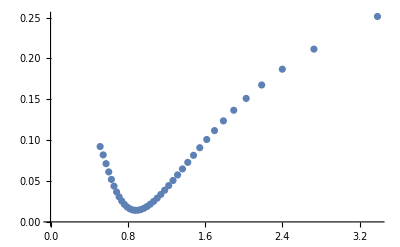

```mathematica
ListPlot[L2]
```

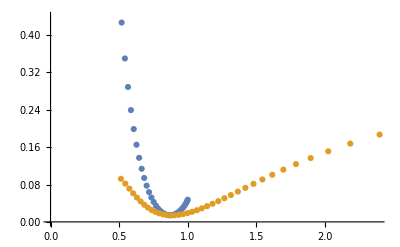

```mathematica
ListPlot[{L1,L2}] (*Don't match at equal τ2 values*)
```

Running test to see how well the values of tr(\wt{C} \wt{A}^{-1})/|\hat{f}(0)|^2 converge as L is increased

```mathematica
L31=Table[
Print[k];
findTrCA11[setL,2*k,k,AMat,CMat11]
,{k,1,31,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

{{0.951072+0.30958 ⅈ,0.0927827-0.0190954 ⅈ,0.0960742991532-0.007804243051211 ⅈ},{0.942985+0.399032 ⅈ,0.0746484-0.015403 ⅈ,0.0759851868376-0.01558916130085 ⅈ},{0.924931+0.456045 ⅈ,0.0615566-0.0208469 ⅈ,0.06200336020169-0.02075788121929 ⅈ},{0.908263+0.504204 ⅈ,0.0499376-0.0237168 ⅈ,0.05025148217636-0.02383473200774 ⅈ},{0.89134+0.546942 ⅈ,0.0398149-0.0250881 ⅈ,0.04001989656478-0.02517542644765 ⅈ},{0.874269+0.586672 ⅈ,0.0309684-0.0249778 ⅈ,0.03111701666957-0.02509285358092 ⅈ},{0.856622+0.624277 ⅈ,0.0233793-0.0237824 ⅈ,0.02348400027538-0.02388445051672 ⅈ},{0.838327+0.660533 ⅈ,0.0170144-0.0217324 ⅈ,0.01708588410052-0.02183472407361 ⅈ},{0.819154+0.695812 ⅈ,0.0118276-0.0191196 ⅈ,0.01187317347884-0.01920971218256 ⅈ},{0.798992+0.73048 ⅈ,0.00774479-0.0161677 ⅈ,0.007768967100684-0.01624907410823 ⅈ},{0.777647+0.764737 ⅈ,0.00465982-0.0130907 ⅈ,0.00466776012955-0.01315835600557 ⅈ},{0.754969+0.798796 ⅈ,0.00244523-0.0100479 ⅈ,0.0024404300597-0.01010279568669 ⅈ},{0.730749+0.832781 ⅈ,0.000956229-0.00716316 ⅈ,0.000942658737019-0.00720345155773 ⅈ},{0.704784+0.86683 ⅈ,0.0000442472-0.00450967 ⅈ,0.0000250881743-0.00453607905208 ⅈ},{0.676813+0.901024 ⅈ,-0.00043447-0.00212072 ⅈ,-0.00045603364765-0.00213290806139 ⅈ},{0.646549+0.93545 ⅈ,-0.000607544+0.0000119008 ⅈ,-0.000628713303172+0.00001274472005 ⅈ}}

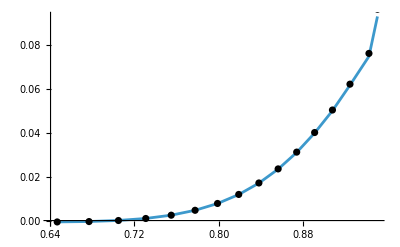

```mathematica
Show[ListLinePlot[Re[L31[[All,{1,2}]]]],ListPlot[Re[L31[[All,{1,3}]]],PlotStyle->{Black}]]
```

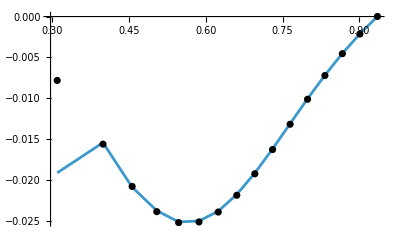

```mathematica
Show[ListLinePlot[Im[L31[[All,{1,2}]]]],ListPlot[Im[L31[[All,{1,3}]]],PlotStyle->{Black}]]
```

```mathematica
L32=Table[
Print[k];
findTrCA21[setL,2*k,k,AMat,CMat21]
,{k,1,31,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

{{0.951072+0.30958 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.942985+0.399032 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.924931+0.456045 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.908263+0.504204 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.89134+0.546942 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.874269+0.586672 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.856622+0.624277 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.838327+0.660533 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.819154+0.695812 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.798992+0.73048 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.777647+0.764737 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.754969+0.798796 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.730749+0.832781 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.704784+0.86683 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.676813+0.901024 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.646549+0.93545 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

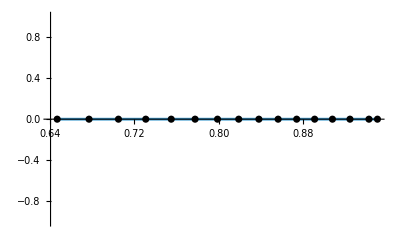

```mathematica
Show[ListLinePlot[Re[L32[[All,{1,2}]]]],ListPlot[Re[L32[[All,{1,3}]]],PlotStyle->{Black}]]
```

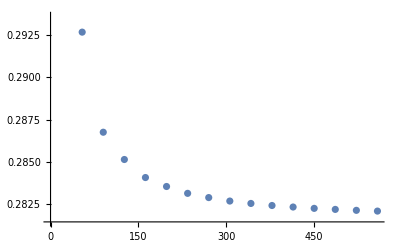

```mathematica
ListPlot[Table[{18*k,L3[[(k-1)/2+1,2]]},{k,1,31,2}]]
```

```mathematica
L33=Table[
Print[k];
findTrCA31[setL,2*k,k,AMat,CMat31]
,{k,1,31,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

{{0.951072+0.30958 ⅈ,-0.117759+0.0492519 ⅈ,-0.1237620004275+0.02026478483613 ⅈ},{0.942985+0.399032 ⅈ,-0.147138+0.0637491 ⅈ,-0.1481142756117+0.06383219625693 ⅈ},{0.924931+0.456045 ⅈ,-0.143803+0.111081 ⅈ,-0.1440945761578+0.110163649888 ⅈ},{0.908263+0.504204 ⅈ,-0.120455+0.151892 ⅈ,-0.1205864121481+0.1517567081473 ⅈ},{0.89134+0.546942 ⅈ,-0.0823542+0.182819 ⅈ,-0.082580158993139+0.18267818205471 ⅈ},{0.874269+0.586672 ⅈ,-0.0356704+0.198864 ⅈ,-0.035821950035242+0.19894554489414 ⅈ},{0.856622+0.624277 ⅈ,0.0134655+0.198797 ⅈ,0.01331096834304+0.19897142757102 ⅈ},{0.838327+0.660533 ⅈ,0.0586719+0.183406 ⅈ,0.058624349143843+0.18368635380143 ⅈ},{0.819154+0.695812 ⅈ,0.0949916+0.155918 ⅈ,0.095020683502614+0.15625220652663 ⅈ},{0.798992+0.73048 ⅈ,0.119095+0.12106 ⅈ,0.11924463652199+0.12140548804469 ⅈ},{0.777647+0.764737 ⅈ,0.130057+0.0842275 ⅈ,0.13029620713438+0.084552813397956 ⅈ},{0.754969+0.798796 ⅈ,0.129112+0.050526 ⅈ,0.12943395702518+0.050789781995817 ⅈ},{0.730749+0.832781 ⅈ,0.119409+0.0238326 ⅈ,0.11977741063394+0.02402542363649 ⅈ},{0.704784+0.86683 ⅈ,0.105211+0.00625925 ⅈ,0.1055957633426+0.006368739859412 ⅈ},{0.676813+0.901024 ⅈ,0.0910534-0.00216321 ⅈ,0.09142671893966-0.00212130279895 ⅈ},{0.646549+0.93545 ⅈ,0.0808541-0.0032824 ⅈ,0.08119537424503-0.00329319486943 ⅈ}}

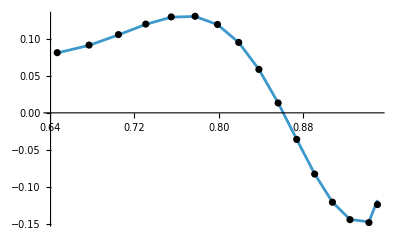

```mathematica
Show[ListLinePlot[Re[L33[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L33],PlotStyle->{Black}]]
```

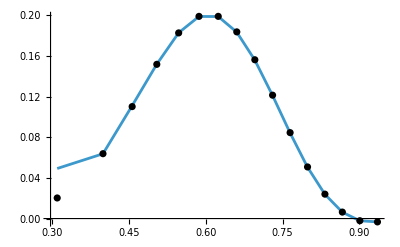

```mathematica
Show[ListLinePlot[Im[L33[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L33],PlotStyle->{Black}]]
```